```mathematica
Integrate[Boole[(x - x1)^2 + (y - y1)^2<r1^2&&(x - x2)^2 + (y - y2)^2<r2^2],{x,Min[x1 - r1, x2 - r2],Max[x1 + r1, x2+ r2]},{y,Min[y1 - r1, y2 - r2],Max[y1 + r1, y2+ r2]}]
```

∫_Min[-r1+x1,-r2+x2]^Max[r1+x1,r2+x2] ∫_Min[-r1+y1,-r2+y2]^Max[r1+y1,r2+y2] Boole[(x-x1)^2+(y-y1)^2<r1^2&&(x-x2)^2+(y-y2)^2<r2^2]ⅆyⅆx

## Preparations for intersection area

```mathematica
R1 = 1;
R2 = 0.5;
```

```mathematica
F1= 2 * ArcCos[(R1^2- R2^2 + d^2)/(2R1 d)];
F2= 2 * ArcCos[(R2^2- R1^2 + d^2)/(2R2 d)];
S1= R1^2 * (F1 - Sin@F1)/2;
S2= R2^2 * (F2 - Sin@F2)/2;
```

```mathematica
Scom = S1 + S2;
```

```mathematica
fun[d_] := 1/2 R1^2 (2 ArcCos[(d^2+R1^2-R2^2)/(2 d R1)]-Sin[2 ArcCos[(d^2+R1^2-R2^2)/(2 d R1)]])+1/2 R2^2 (2 ArcCos[(d^2-R1^2+R2^2)/(2 d R2)]-Sin[2 ArcCos[(d^2-R1^2+R2^2)/(2 d R2)]])
```

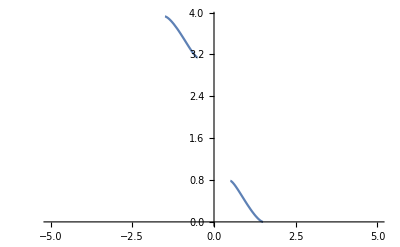

```mathematica
Plot[fun[d], {d, -5 ,5}]
```

## Intersection area of two circles

```mathematica
InterArea[r1_, r2_, d_] := Piecewise[
{{1/2 r1^2 (2 ArcCos[(d^2+r1^2-r2^2)/(2 Abs@d r1)]-Sin[2 ArcCos[(d^2+r1^2-r2^2)/(2 Abs@d r1)]])+1/2 r2^2 (2 ArcCos[(d^2-r1^2+r2^2)/(2Abs@d r2)]-Sin[2 ArcCos[(d^2-r1^2+r2^2)/(2 Abs@d r2)]]), Abs@d ≤ (r1 + r2) && Abs@d ≥ Max[r1, r2]}, {Min[r1, r2]^2 * π,Abs@d≤Max[r1, r2]}}] (*Зависимость площади перекрытия двух кругов от их радиусов и расстояния между ними*)
```

```mathematica
fun1[r1_, r2_, d_] := 1/2 r1^2 (2 ArcCos[(d^2+r1^2-r2^2)/(2d r1)]-Sin[2 ArcCos[(d^2+r1^2-r2^2)/(2d r1)]])+1/2 r2^2 (2 ArcCos[(d^2-r1^2+r2^2)/(2d r2)]-Sin[2 ArcCos[(d^2-r1^2+r2^2)/(2 d r2)]]);
```

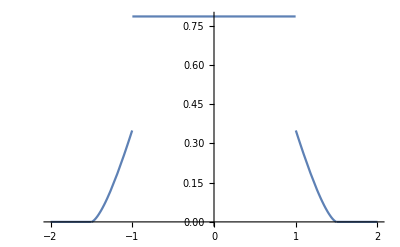

0.350767

```mathematica
Plot[InterArea[R1, R2, dis], {dis, -2, 2}]
InterArea[R1, R2, 1]//N
```

## Movement at a distance

```mathematica
Manipulate[Plot[InterArea[r1, r2, √(r^2 + b^2)], {r, -5, 5}, PlotRange->{{-5, 5}, {0, 5}}], {b,0, 5}, {r1, 0, 5}, {r2, 0, 5}]
```